```mathematica
(* This file looks at the radial distribution function for the same simulation of two sizes of hard spheres as I did in Smoldyn but with SpringSaLaD.  The crowding2size.nb file has to be run first so that the final figure works. *)
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/sandrews/SSA/INI/Smoldyn/SpringSaLaD

```mathematica
maxradius=20
volume=1000000
r1=2.5
r2=4
number1=6000
number2=500
```

20

1000000

2.5

4

6000

500

```mathematica
volfraction=N[(number1*4/3*Pi*r1^3+number2*4/3*Pi*r2^3)/volume]
```

0.52674

```mathematica
(* Load and look at data *)
```

```mathematica
simdata=Import["results2sizeSSLD.csv","CSV"];
```

```mathematica
simdata[[1;;10]]
```

{{ID,100000000,2.5,RED,38.7441,-25.0975,56.2192},{ID,100010000,2.5,RED,-20.1684,-26.0018,14.2438},{ID,100020000,2.5,RED,-30.1805,47.3607,33.6699},{ID,100030000,2.5,RED,19.2908,-6.59834,17.3198},{ID,100040000,2.5,RED,37.1616,11.6395,2.92556},{ID,100050000,2.5,RED,-21.9881,33.0747,14.5593},{ID,100060000,2.5,RED,-46.9707,-21.2072,43.3802},{ID,100070000,2.5,RED,11.7993,24.587,14.5664},{ID,100080000,2.5,RED,-42.4345,4.76334,24.9727},{ID,100090000,2.5,RED,6.02131,-17.0368,55.9596}}

```mathematica
simdata1=Transpose[Drop[Transpose[simdata],4]];
```

```mathematica
{Min[simdata1[[All,1]]],Max[simdata1[[All,1]]]}
{Min[simdata1[[All,2]]],Max[simdata1[[All,2]]]}
{Min[simdata1[[All,3]]],Max[simdata1[[All,3]]]}
```

{-47.4998,47.4996}

{-47.4996,47.498}

{2.50158,97.4998}

```mathematica
(* Computes the radial distribution function about a single point *)
rdfpt[x_,data_,distmax_,bins_]:=Last[Last[Module[{bin,dist,hist,i},
hist=Table[0,{bins}];
For[i=1,i<=Length[data],i++,{
dist=Sqrt[(data[[i,1]]-x[[1]])^2+(data[[i,2]]-x[[2]])^2+(data[[i,3]]-x[[3]])^2];
bin=Floor[dist*bins/distmax];
If[bin>0&&bin≤bins,hist[[bin]]++]}]
Return[hist]]]]
```

```mathematica
ans=rdfpt[{0,0,50},simdata1,10,10]
```

{0,1,0,1,2,4,8,5,10,7}

```mathematica
nbin=100
```

100

```mathematica
hist=Table[0,{nbin}];
For[i=number1+1,i≤number1+number2,i++,{
x=simdata1[[i]];
If[x[[1]]>-30&&x[[1]]<30&&x[[2]]>-30&&x[[2]]<30&&x[[3]]>30&&x[[3]]<70,hist+=rdfpt[x,simdata1[[1;;number1]],maxradius,nbin]]}]
```

```mathematica
hist
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,26,356,199,160,108,70,60,66,55,46,58,40,40,54,54,65,64,80,88,100,110,153,158,159,195,226,200,189,187,159,150,198,145,162,175,172,181,160,176,192,220,236,270,285,267,284,294,301,296,304,314,322,295,355,337,336,342,364,336,395,363,365,400,446,402,473,443,463,435,450}

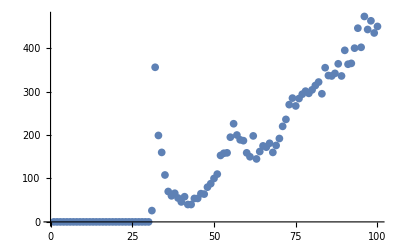

```mathematica
ListPlot[hist]
```

```mathematica
binwidth=N[maxradius/nbin]
```

0.2

```mathematica
xvector=Table[i,{i,binwidth/2,maxradius-binwidth/2,binwidth}]
```

{0.1,0.3,0.5,0.7,0.9,1.1,1.3,1.5,1.7,1.9,2.1,2.3,2.5,2.7,2.9,3.1,3.3,3.5,3.7,3.9,4.1,4.3,4.5,4.7,4.9,5.1,5.3,5.5,5.7,5.9,6.1,6.3,6.5,6.7,6.9,7.1,7.3,7.5,7.7,7.9,8.1,8.3,8.5,8.7,8.9,9.1,9.3,9.5,9.7,9.9,10.1,10.3,10.5,10.7,10.9,11.1,11.3,11.5,11.7,11.9,12.1,12.3,12.5,12.7,12.9,13.1,13.3,13.5,13.7,13.9,14.1,14.3,14.5,14.7,14.9,15.1,15.3,15.5,15.7,15.9,16.1,16.3,16.5,16.7,16.9,17.1,17.3,17.5,17.7,17.9,18.1,18.3,18.5,18.7,18.9,19.1,19.3,19.5,19.7,19.9}

```mathematica
Length[xvector]
```

100

```mathematica
rdf=Table[N[hist[[i]]/(i^3-(i-1)^3)],{i,1,Length[hist]}]
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.00931566,0.119583,0.0627958,0.04752,0.0302436,0.0185136,0.0150113,0.0156435,0.0123679,0.00982696,0.0117862,0.00774144,0.00738144,0.00951207,0.00908938,0.0104653,0.00986589,0.0118186,0.0124699,0.0136036,0.0143772,0.0192284,0.0191075,0.0185164,0.0218831,0.0244562,0.0208834,0.0190543,0.0182137,0.0149703,0.01366,0.0174495,0.0123731,0.0133918,0.0140213,0.0133634,0.0136429,0.0117053,0.0125027,0.0132496,0.0147542,0.0153876,0.0171222,0.017585,0.0160351,0.0166072,0.0167455,0.0167046,0.0160113,0.0160329,0.0161514,0.016159,0.0144473,0.0169718,0.0157322,0.0153208,0.0152359,0.0158474,0.0142997,0.0164371,0.0147735,0.014532,0.015583,0.0170054,0.015005,0.0172874,0.0158571,0.0162348,0.0149449,0.015151}

```mathematica
rdf=rdf/rdf[[-1]]
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.614854,7.89277,4.14466,3.13643,1.99615,1.22194,0.990776,1.03251,0.816308,0.648601,0.777917,0.510952,0.487191,0.627818,0.599919,0.690733,0.65117,0.780053,0.82304,0.897867,0.948928,1.26911,1.26114,1.22212,1.44433,1.61417,1.37835,1.25763,1.20214,0.988076,0.901588,1.15171,0.81665,0.883885,0.925438,0.882012,0.90046,0.772577,0.825204,0.874503,0.973811,1.01562,1.1301,1.16065,1.05835,1.09611,1.10524,1.10254,1.05678,1.05821,1.06603,1.06653,0.953556,1.12018,1.03836,1.01121,1.0056,1.04597,0.943812,1.08489,0.975085,0.959144,1.02851,1.12239,0.990366,1.14101,1.0466,1.07153,0.986394,1.}

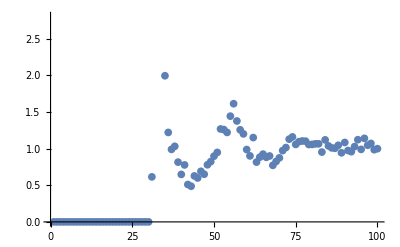

```mathematica
ListPlot[rdf]
```

```mathematica
rdfxy=Transpose[{xvector,rdf}];
```

```mathematica
h=0.4
```

0.4

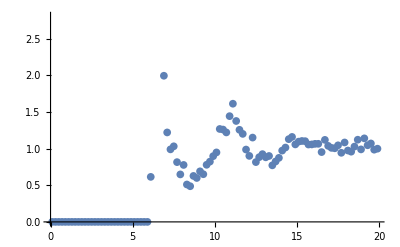

```mathematica
ListPlot[rdfxy]
```

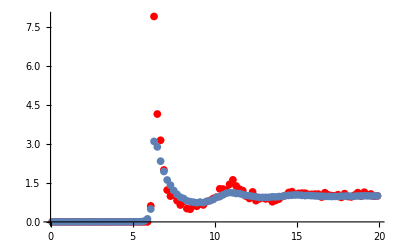

```mathematica
Show[{ListPlot[rdfxy,PlotStyle->Red,PlotRange->All],ListPlot[simdata2xy]}]
```